# Dynamics of Interacting Pressure-less Dark Matter and Dark Energy with a Non-Linear Quadratic EoS

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations of interating dark energy, x, and dark matter, z, and the Hubble expansion, y*)
(*de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z[x,q1,ℛ]
de2:=y'=-y^2-(1/6)*(z[x,q1,ℛ]-2*x)
de3:=z'=-3*y*z[x,q1,ℛ]*(1-q1*(x-ℛ)*(1-x))*)
```

```mathematica
(*Solve for the fixed points of the system*)
(*FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]*)
```

```mathematica
(*Define z(x) and the first integral cz*)
α=0.5;

cz=(1/(q1*(1-ℛ))*Log[ℛ(1-α)/(α-ℛ)]-(ℛ/α)*(1+0.3111/0.6889))

z[x_,q1_,ℛ_]=(-q1)*x/q1+(1/(q1*(1-ℛ)))*Log[(x-ℛ)/(1-x)]-cz
```

-2.90318 ℛ+Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
de1t:=x'[t]==-3*y[t]*q1*(x[t]-ℛ)*(1-x[t])*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)
de2t:=y'[t]==-y[t]^2-(1/6)*(((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)-2*x[t])
de3t:=z'[t]==-3*y[t]*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)*(1-q1*(x[t]-ℛ)*(1-x[t]))
```

```mathematica
(*The remaining equation when y' = y = 0, which can be solved to find the number of Einstein points admitted by the system*)
f[x_,q1_,ℛ_]=z[x,q1,ℛ]-2*x
```

-3 x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
(*Find the limit of f when x -> ℛ*)
Limit[f[x,q1,ℛ],x->ℛ, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

-∞

```mathematica
(*Find the limit of f when x -> 1*)
Limit[f[x,q1,ℛ],x->1, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

∞

```mathematica
(*Find derivative of f(x) with respect to x*)
fDeriv[x_,q1_,ℛ_]=Simplify[D[f[x,q1,ℛ],x]]
```

-3-1/(q1 (-1+x) (x-ℛ))

```mathematica
(*Solve f'(x)=0 for q1 in limiting case*)
q1Lim[x_,ℛ_]=Solve[fDeriv[x,q1,ℛ]==0,q1]
```

{{q1→-1/(3 (-1+x) (x-ℛ))}}

```mathematica
q1Lim[x_,ℛ_]=q1/.q1Lim[x,ℛ]
```

{-1/(3 (-1+x) (x-ℛ))}

## Plots

### No Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=15;
```

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[x/3+z[x,q1,ℛ]/3];
```

```mathematica
(*Plot the FFS*)
FFS0EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {Black, Thick}];
```

Plot::plln: Limiting value ℛ in {x,ℛ,1} is not a machine-sized real number.

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.1}, {x,y},{t,0,40}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== .1, x[0]== .99}, {x,y},{t,0,40}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]== 0.1, x[0]==0.2}, {x,y},{t,0,20}]; 
Traj0EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3}, {t,0,20}, PlotStyle -> {{Gray, Opacity[0.75]}}]];


(*Plot*)
(*Show[FFS0EPts,Traj0EPts]*)
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{x'[t]==-45 (1-x[«1»]) (2.90318 ℛ-1/15 Power[«2»] Log[«1»]+1/15 Power[«2»] Log[«1»]-x[«1»]) (-ℛ+x[t]) y[t],y'[t]==1/6 (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])-y[«1»]^2,y[0]==0.1,x[0]==0.1},{x,y},{t,0,40}],NDSolve[«1»,{x,y},{t,0,40}],NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408163 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{x'[0.000408163]==-45 (1-x[«1»]) (2.90318 ℛ-1/15 Power[«2»] Log[«1»]+1/15 Power[«2»] Log[«1»]-x[«1»]) (-ℛ+x[0.000408163]) y[0.000408163],y'[0.000408163]==1/6 (Times[«2»]+Times[«3»]+Times[«3»]+Times[«2»])-y[«1»]^2,y[0]==0.1,x[0]==0.1},{x,y},«1»],«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[«1»],NDSolve[«1»],NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{FFS,-FFS},{x,ℛ,1},PlotStyle→{Black,Thick}],].

Show[Plot[{FFS,-FFS},{x,ℛ,1},PlotStyle→{Black,Thick}],-Graphics-]

### 2 Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=7;
```

```mathematica
ℛ=0.01;
q1=7
```

7

```mathematica
(*Substitute q1Lim into f(x)=0 and solve for x*)
x1=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]

x2=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]
```

0.0378015

0.841311

```mathematica
(*Find corresponding q1 values*)
q1Lim1=q1Lim[x1,ℛ]
q1Lim2=q1Lim[x2,ℛ]
```

{12.4608}

{2.52678}

```mathematica
xTwoEinsteinPointsq1i=FindRoot[f[x,q1,ℛ]==0,{x,0.02}]
xTwoEinsteinPointsq1ii=FindRoot[f[x,q1,ℛ]==0,{x,0.13}]
xTwoEinsteinPointsq1iii=FindRoot[f[x,q1,ℛ]==0,{x,0.99}]
```

{x→0.0232042}

{x→0.138837}

{x→1.-9.85008×10^-21 ⅈ}

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsq1={x/.xTwoEinsteinPointsq1i,x/.xTwoEinsteinPointsq1ii,x/.xTwoEinsteinPointsq1iii}
```

{0.0232042,0.138837,1.-9.85008×10^-21 ⅈ}

```mathematica
(*Calculate the Z values of the Einstein points*)
zTwoEinsteinPointsq1=z[xTwoEinsteinPointsq1,q1,ℛ]
```

{0.0464084,0.277674,2.-1.28071×10^-14 ⅈ}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[1]={xTwoEinsteinPointsq1[[1]],0,zTwoEinsteinPointsq1[[1]]}
EinsteinFP[2]={xTwoEinsteinPointsq1[[2]],0,zTwoEinsteinPointsq1[[2]]}
EinsteinFP[3]={xTwoEinsteinPointsq1[[3]],0,zTwoEinsteinPointsq1[[3]]}
```

{0.0232042,0,0.0464084}

{0.138837,0,0.277674}

{1.-9.85008×10^-21 ⅈ,0,2.-1.28071×10^-14 ⅈ}

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[x/3+z[x,q1,ℛ]/3];
```

```mathematica
(*Plot the FFS*)
FFS2EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {{Darker[Green], Thick}}];
```

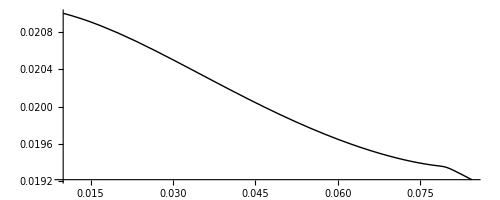

```mathematica
(*Plot the CFS*)
CFS2EPts=NDSolve[{de1t,de2t, y[0]== 0.01, x[0]==0.021}, {x,y},{t,0,30}];

CFS2EPts=ParametricPlot[Evaluate[{y[t],x[t]}/.{CFS2EPts}, {t,0,50}, PlotStyle -> {{Black, Thick}}]]
```

```mathematica
xTwoEinsteinPointsq1[[1]]
```

0.0232042

```mathematica
(*Plot the fixed points*)
FPShow2EPts=ListPlot[{{xTwoEinsteinPointsq1[[1]],0},{xTwoEinsteinPointsq1[[2]],0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating region*)
Acc2EPts=ContourPlot[{z[x,q1,ℛ]-2*x==0},{x,ℛ,1},{y,-1,1},ContourStyle->{Red, Thick}];
```

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.45}, {x,y},{t,0,40}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== -.1, x[0]== .99}, {x,y},{t,0,40}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]== 0.1, x[0]==0.2}, {x,y},{t,0,20}]; 
Traj2EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3}, {t,0,20}, PlotStyle -> {{Gray, Opacity[0.75]}}]];
```

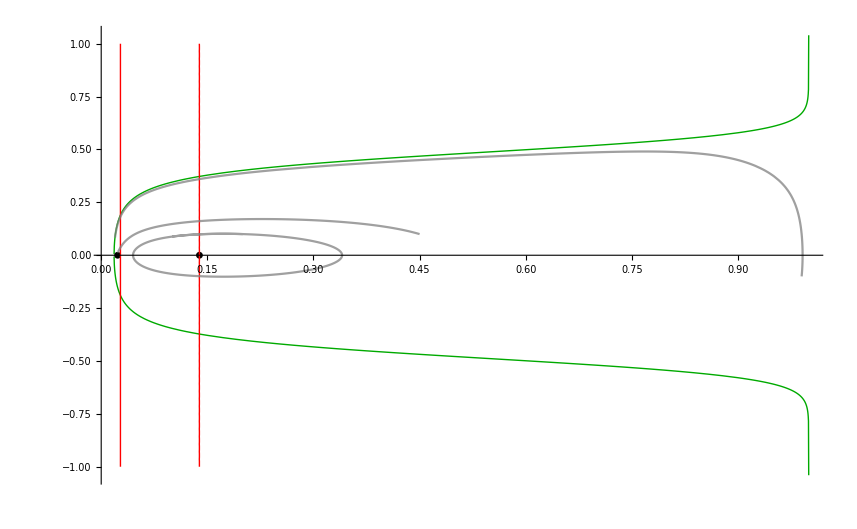

```mathematica
(*Plot all components of the phase space*)
Show[FFS2EPts,FPShow2EPts,Acc2EPts,Traj2EPts]
```